```mathematica
<<mf23.m
```

```mathematica
Clear[c];
Clear[e];
ψ[z_]:=PolyGamma[z]; (* RHS is Mathematica-speak for the digamma function. *)
α[m_]:=(1/2)*(1/2-1/m);
β[m_]:=(1/2)*(1/2+1/m);
c[m_,ν_]:=Pochhammer[α[m],ν]*Pochhammer[β[m],ν]/(ν!)^2;
e[m_,ν_]:=Sum[1/(α[m]+p)+1/(β[m]+p)-2/(1+p),{p,0,ν-1}];
F[n_,m_,u_]:=Series[Sum[c[m,ν]*u^ν,{ν,0,n+1}],{u,0,n}];
Fstar[n_,m_,u_]:=Sum[c[m,ν]*e[m,ν]*u^ν,{ν,1,n}];
logA[m_]:=-2ψ[1]+ψ[1-α[m]]+ψ[1-β[m]]-π*Sec[π/m]; (* Raleigh's eq (10) *)
A[m_]:=Exp[logA[m]];
λ[m_]:=2*Cos[π/m]
```

#### From Raleigh p 108 eq 6 (abbreviating the F, F* inputs): 2πiτ/λ_m= - log J + F*(1/J)/F(1/J) - πi(b-bar) = - log J + F*(1/J)/F(1/J) + log A(m) = log(1/J) + F*(1/J)/F(1/J) + log A(m) . Taking exponentials, x_m =(1/J) exp( (F*(1/J)/F(1/J) ) A(m). Then x_m/A(m) = (1/J) exp( F*(1/J)/F(1/J). Viewing the RHS above as a power series in 1/J, invert it and get 1/J = a power series in x_m (Raleigh’s eq. 12 ), so J = 1/(the inverted power series)--but the uniformizing variable is X_m = x_m/A(m) ; not x_m. Below I inadvertently mixed the variables x and X, but tests indicate that this has no effect. Whether or not I replace x by X, the output is written (correctly ) in terms o f X.

```mathematica
ex[n_,m_,oneOverJ_]:=
Module[{a0,a1,a2,a3,a4,a5,a6,K},
a0=Series[Fstar[n,m,oneOverJ]/F[n,m,oneOverJ],{oneOverJ,0,n}];

a1=Series[Exp[a0],{oneOverJ,0,n}];

a2=Collect[oneOverJ*a1,oneOverJ];

a3=Series[a2,{oneOverJ,0,n}];
Return[a3]];

J[n_,m_,X_]:=Collect[Normal[Series[1/InverseSeries[ex[n,m,X],X],{X,0,n}]],X];


recipJ[n_,m_,X_]:=Collect[Normal[InverseSeries[ex[n,m,X],X]],X];
```

#### The weight of f_λ at Hecke rank m is determined in Theorem 7 of Berndt in my paper; with outer exponent j = 1/(m - 2) . By Th 7 my draft, the weight after omitting the outer exponent, as below, is 4.

```mathematica
fλNew3[n_,m_,X_]:= (* n = nbr of terms, k = weight, m = Hecke rank. *)
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m,X]; 
djay=X*D[jay,X];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-1);
answer=Collect[Series[(numerator/denominator),{X,0,n}],X];
Return[answer]]
```

```mathematica
fi[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Series[(numerator/denominator)^(1/(m-2)),{x,0,n}];
Return[answer]]
```

#### The weight of f_λ is not fixed at four : weights are determined in Theorem 7 of Berndt in my paper; f_λ has weight 4 only for m = 3. From th 7, to get weight k, replace the 1/(m-2) with k/4. The weight of f_i is 2m/(m-2), so, the weight of fiNoOuterExponent is 2m. To fix the weight at 6, raise it to the power 6/2m = 3/m. It recovers Serre’s E3 (p93).

```mathematica
fiNoOuterExponent[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Series[(numerator/denominator),{x,0,n}];
Return[answer]]
```

```mathematica
Print[N[fλNew3[10,3,x]/.x->x/A[3]]];
Print[1+Sum[240*DivisorSigma[3,n]*x^n,{n,1,10}]];
Print["========================================================="];
srs=Normal[Series[fλNew3[10,3,x]^(3/2),{x,0,10}]];
Print[N[srs/.x->x/A[3]]];
Print[1-Sum[504*DivisorSigma[5,n]*x^n,{n,1,10}]];
Print["========================================================="];
srs=Normal[Series[fiNoOuterExponent[10,3,x]^(3/3),{x,0,10}]];
Print[N[srs/.x->x/A[3]]];
Print[1-Sum[504*DivisorSigma[5,n]*x^n,{n,1,10}]];
```

1.+240. x+2160. x^2+6720. x^3+17520. x^4+30240. x^5+60480. x^6+82560. x^7+140400. x^8+181680. x^9+272160. x^10

1+240 x+2160 x^2+6720 x^3+17520 x^4+30240 x^5+60480 x^6+82560 x^7+140400 x^8+181680 x^9+272160 x^10

=========================================================

1.+360. x+24840. x^2-465120. x^3+5.74175×10^7 x^4-6.80028×10^9 x^5+9.3089×10^11 x^6-1.39402×10^14 x^7+2.22503×10^16 x^8-3.72396×10^18 x^9+6.46516×10^20 x^10

1-504 x-16632 x^2-122976 x^3-532728 x^4-1575504 x^5-4058208 x^6-8471232 x^7-17047800 x^8-29883672 x^9-51991632 x^10

=========================================================

-1.+504. x+16632. x^2+122976. x^3+532728. x^4+1.5755×10^6 x^5+4.05821×10^6 x^6+8.47123×10^6 x^7+1.70478×10^7 x^8+2.98837×10^7 x^9+5.19916×10^7 x^10

1-504 x-16632 x^2-122976 x^3-532728 x^4-1575504 x^5-4058208 x^6-8471232 x^7-17047800 x^8-29883672 x^9-51991632 x^10

```mathematica
fλcubed[n_,m_,X_]:= (* n = nbr of terms, k = weight, m = Hecke rank. *)
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m,X]; 
djay=X*D[jay,X];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-1);
answer=Collect[Series[(numerator/denominator)^3,{X,0,n}],X];
Return[answer]]
```

```mathematica
diamondCuspFrm[n_,m_,X_]:=
Collect[fλcubed[n,m,X]*recipJ[n,m,X],X]
```

```mathematica
stream=OpenWrite["run24apr21no2"];
start=SessionTime[];
Clear[x];
For[m=2,m<300,m++;
expansion=fλNew3[100,m,x];
Write[stream,{m,expansion}]];
Close[stream];
Print["elapsed seconds = ",SessionTime[]-start]
```

elapsed seconds = 34057.08102

```mathematica
stream=OpenWrite["run4may1no5"];
start=SessionTime[];
Clear[x];
For[m=2,m<200,m++;
srs=Series[fλNew3[30,m,x]^(3/2),{x,0,30}];(* wt 6 *)
srs=Normal[srs];
srs=Collect[srs,x];
Write[stream,{m,srs}]];
Close[stream];
Print["elapsed seconds = ",SessionTime[]-start]
```

elapsed seconds = 61.88122

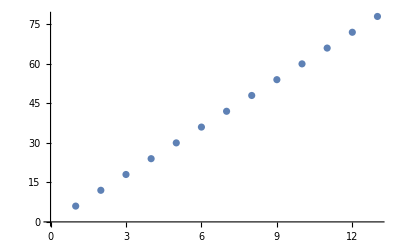

{{1,6},{2,12},{3,18},{4,24},{5,30},{6,36},{7,42},{8,48},{9,54},{10,60},{11,66},{12,72},{13,78}}

```mathematica
stream=OpenRead["run24apr21no2"];
list=ReadList[stream];
Close[stream];
(*
wstream=OpenWrite["run30apr21no21"];
*)
degrees={};
For[n=0,n<13,n++;
data={};
For[k=2,k<Length[list],k++;
m=list[[k,1]];
srs=list[[k,2]];
srs=(srs/.x->x*2^6*m^3);
ns=Normal[srs]; (*need srs=list[[k,2]], ns = Normal[srs], etc. *)
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,n];
AppendTo[data,{m,cf*m^(3*n)}]

]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];
(*
Write[wstream,{n,ip}];
*)
AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Print[degrees];
(*
Close[wstream]
*)
```

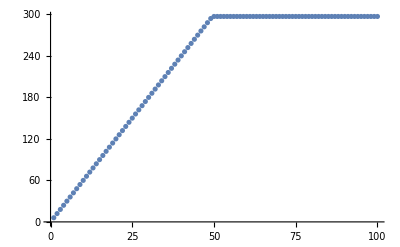

{{1,6},{2,12},{3,18},{4,24},{5,30},{6,36},{7,42},{8,48},{9,54},{10,60},{11,66},{12,72},{13,78},{14,84},{15,90},{16,96},{17,102},{18,108},{19,114},{20,120},{21,126},{22,132},{23,138},{24,144},{25,150},{26,156},{27,162},{28,168},{29,174},{30,180},{31,186},{32,192},{33,198},{34,204},{35,210},{36,216},{37,222},{38,228},{39,234},{40,240},{41,246},{42,252},{43,258},{44,264},{45,270},{46,276},{47,282},{48,288},{49,294},{50,297},{51,297},{52,297},{53,297},{54,297},{55,297},{56,297},{57,297},{58,297},{59,297},{60,297},{61,297},{62,297},{63,297},{64,297},{65,297},{66,297},{67,297},{68,297},{69,297},{70,297},{71,297},{72,297},{73,297},{74,297},{75,297},{76,297},{77,297},{78,297},{79,297},{80,297},{81,297},{82,297},{83,297},{84,297},{85,297},{86,297},{87,297},{88,297},{89,297},{90,297},{91,297},{92,297},{93,297},{94,297},{95,297},{96,297},{97,297},{98,297},{99,297},{100,297}}

```mathematica
stream=OpenRead["run24apr21no2"];
list=ReadList[stream];
Close[stream];
(*
wstream=OpenWrite["run30apr21no21"];
*)
degrees={};
For[n=0,n<100,n++;
data={};
For[k=0,k<Length[list],k++;
m=list[[k,1]];
srs=list[[k,2]];
srs=(srs/.x->x*2^6*m^3);
ns=Normal[srs]; (*need srs=list[[k,2]], ns = Normal[srs], etc. *)
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,n];
AppendTo[data,{m,cf*m^(3*n)}]

]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];
(*
Write[wstream,{n,ip}];
*)
AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Print[degrees];
(*
Close[wstream]
*)
```

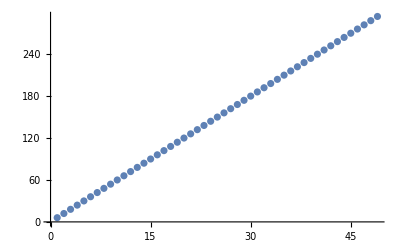

{{1,6},{2,12},{3,18},{4,24},{5,30},{6,36},{7,42},{8,48},{9,54},{10,60},{11,66},{12,72},{13,78},{14,84},{15,90},{16,96},{17,102},{18,108},{19,114},{20,120},{21,126},{22,132},{23,138},{24,144},{25,150},{26,156},{27,162},{28,168},{29,174},{30,180},{31,186},{32,192},{33,198},{34,204},{35,210},{36,216},{37,222},{38,228},{39,234},{40,240},{41,246},{42,252},{43,258},{44,264},{45,270},{46,276},{47,282},{48,288},{49,294}}

run30apr21no21

```mathematica
stream=OpenRead["run24apr21no2"];
list=ReadList[stream];
Close[stream];

wstream=OpenWrite["run30apr21no21"];

degrees={};
For[n=0,n<49,n++;
data={};
For[k=0,k<Length[list],k++;
m=list[[k,1]];
srs=list[[k,2]];
srs=(srs/.x->x*2^6*m^3);
ns=Normal[srs]; (*need srs=list[[k,2]], ns = Normal[srs], etc. *)
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,n];
AppendTo[data,{m,cf*m^(3*n)}]

]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];

Write[wstream,{n,ip}];

AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Print[degrees];

Close[wstream]
```

```mathematica
stream=OpenRead["run30apr21no21"];
list=ReadList[stream];
Close[stream];
numerators={};
denominators={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
fim=factorIntoMonics[poly];
numericalterm=fim[[1]];
numerator=Numerator[numericalterm];
denominator=Denominator[numericalterm];
AppendTo[numerators,numerator];
AppendTo[denominators,denominator]];
Print["numerators:"];Print[numerators];
Print["denominators:"];Print[denominators]
```

numerators:

{16,112,448,1136,2016,3136,5504,9328,12112,14112,21312,31808,35168,38528,56448,74864,78624,84784,109760,143136,154112,149184,194688,261184,252016,246176,327040,390784,390240,395136,476672,599152,596736,550368,693504,859952,810464,768320,984704,1175328,1102752,1078784,1272128,1513152,1526112,1362816,1661184,2096192,1887888}

denominators:

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Print[numerators/16]
```

{1,7,28,71,126,196,344,583,757,882,1332,1988,2198,2408,3528,4679,4914,5299,6860,8946,9632,9324,12168,16324,15751,15386,20440,24424,24390,24696,29792,37447,37296,34398,43344,53747,50654,48020,61544,73458,68922,67424,79508,94572,95382,85176,103824,131012,117993}

```mathematica
stream=OpenWrite["run4may1no5"];
start=SessionTime[];
Clear[x];
For[m=2,m<200,m++;
srs=Series[fλNew3[30,m,x]^(3/2),{x,0,30}];(* wt 6 *)
srs=Normal[srs];
srs=Collect[srs,x];
Write[stream,{m,srs}]];
Close[stream];
Print["elapsed seconds = ",SessionTime[]-start]
```

elapsed seconds = 61.88122

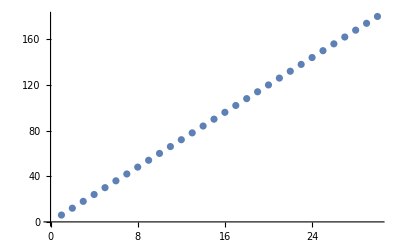

{{1,6},{2,12},{3,18},{4,24},{5,30},{6,36},{7,42},{8,48},{9,54},{10,60},{11,66},{12,72},{13,78},{14,84},{15,90},{16,96},{17,102},{18,108},{19,114},{20,120},{21,126},{22,132},{23,138},{24,144},{25,150},{26,156},{27,162},{28,168},{29,174},{30,180}}

run4may1no6

```mathematica
stream=OpenRead["run4may1no5"];
list=ReadList[stream];
Close[stream];

wstream=OpenWrite["run4may1no6"];

degrees={};
For[n=0,n<30,n++;
data={};
For[k=0,k<Length[list],k++;
m=list[[k,1]];
srs=list[[k,2]];
srs=(srs/.x->x*2^6*m^3);
ns=Normal[srs]; (*need srs=list[[k,2]], ns = Normal[srs], etc. *)
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,n];
AppendTo[data,{m,cf*m^(3*n)}]

]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];

Write[wstream,{n,ip}];

AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Print[degrees];

Close[wstream]
```

```mathematica
stream=OpenRead["run4may1no6"];
list=ReadList[stream];
Close[stream];
numerators={};
denominators={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
fim=factorIntoMonics[poly];
numericalterm=fim[[1]];
numerator=Numerator[numericalterm];
denominator=Denominator[numericalterm];
AppendTo[numerators,numerator];
AppendTo[denominators,denominator]];
Print["numerators:"];Print[numerators/8];
Print["denominators:"];Print[denominators]
```

numerators:

{3,33,220,993,3234,8052,16632,31713,59095,103158,162132,242292,370458,554664,761448,1014753,1421046,1956669,2477772,3104118,4103264,5314716,6428136,7737972,9768333,12252702,14416408,16690344,20509962,25170552}

denominators:

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}